```mathematica
ClearAll["Global`*"];

Nc = 6;
EJ = .;

η = 1/6*SparseArray[{
{i_,i_}:>2*(L[[i]]+L[[i+1]])/EJ[[i]],
{i_,j_}:>L[[i]]/EJ[[i]]/; i-j==1,
{i_,j_}:>L[[i+1]]/EJ[[i]]/; i-j==-1
},{Nc-1, Nc-1}];//Normal//Quiet

F = -1/24* Table[Q[[i]]*(L[[i]]/EJ[[i]])^3+Q[[i+1]]*(L[[i+1]]/EJ[[i+1]])^3, {i ,Nc-1}];//Quiet

MatrixForm[η]
MatrixForm[F]
```

((L⟦1⟧+L⟦2⟧)/(3 EJ⟦1⟧) | L⟦2⟧/(6 EJ⟦1⟧) | 0 | 0 | 0
L⟦2⟧/(6 EJ⟦2⟧) | (L⟦2⟧+L⟦3⟧)/(3 EJ⟦2⟧) | L⟦3⟧/(6 EJ⟦2⟧) | 0 | 0
0 | L⟦3⟧/(6 EJ⟦3⟧) | (L⟦3⟧+L⟦4⟧)/(3 EJ⟦3⟧) | L⟦4⟧/(6 EJ⟦3⟧) | 0
0 | 0 | L⟦4⟧/(6 EJ⟦4⟧) | (L⟦4⟧+L⟦5⟧)/(3 EJ⟦4⟧) | L⟦5⟧/(6 EJ⟦4⟧)
0 | 0 | 0 | L⟦5⟧/(6 EJ⟦5⟧) | (L⟦5⟧+L⟦6⟧)/(3 EJ⟦5⟧))

(1/24 (-(L⟦1⟧^3 Q⟦1⟧)/EJ⟦1⟧^3-(L⟦2⟧^3 Q⟦2⟧)/EJ⟦2⟧^3)
1/24 (-(L⟦2⟧^3 Q⟦2⟧)/EJ⟦2⟧^3-(L⟦3⟧^3 Q⟦3⟧)/EJ⟦3⟧^3)
1/24 (-(L⟦3⟧^3 Q⟦3⟧)/EJ⟦3⟧^3-(L⟦4⟧^3 Q⟦4⟧)/EJ⟦4⟧^3)
1/24 (-(L⟦4⟧^3 Q⟦4⟧)/EJ⟦4⟧^3-(L⟦5⟧^3 Q⟦5⟧)/EJ⟦5⟧^3)
1/24 (-(L⟦5⟧^3 Q⟦5⟧)/EJ⟦5⟧^3-(L⟦6⟧^3 Q⟦6⟧)/EJ⟦6⟧^3))

```mathematica
L = {3.000,4.500,4.000,5.000,6.150,4.000};
EJ=SparseArray[{i_}:>1, {Nc}]//Normal;
```

```mathematica
X=0*Table[j,Nc];
For[i=1, i<= Nc, i++,
Q=0*Table[j,Nc];
Q[[i]]=1;
X[[i]] = LinearSolve[η, F];
X[[i]] = PrependTo[X[[i]],0];
X[[i]] = AppendTo[X[[i]],0];
]
X = Transpose[X];
MatrixForm[%]
```

(0 | 0 | 0 | 0 | 0 | 0
-0.491337 | -1.19322 | 0.24874 | -0.114884 | 0.0482668 | -0.00577194
0.13779 | -1.08509 | -0.829133 | 0.382948 | -0.160889 | 0.0192398
-0.0328526 | 0.258714 | -0.756016 | -1.49828 | 0.62948 | -0.0752758
0.00803761 | -0.0632961 | 0.184964 | -1.16254 | -2.13742 | 0.255601
-0.00243504 | 0.0191759 | -0.0560359 | 0.352197 | -2.21709 | -0.865613
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
R=Array[0, {Nc, Nc}];
For[i=1, i<= Nc, i++,
For[j=1, j<=Nc, j++,
Q=0*Table[k,Nc];
Q[[j]]=1;
R[[i,j]]= (X[[i+1,j]]- X[[i,j]])/L[[i]]+Q[[i]]*L[[i]]/2
]
]
MatrixForm[R]
```

(1.33622 | -0.397741 | 0.0829133 | -0.0382948 | 0.0160889 | -0.00192398
0.139806 | 2.27403 | -0.239527 | 0.110629 | -0.0464792 | 0.00555817
-0.0426606 | 0.335952 | 2.01828 | -0.470308 | 0.197592 | -0.0236289
0.00817805 | -0.0644021 | 0.188196 | 2.56715 | -0.553379 | 0.0661753
-0.00170287 | 0.0134101 | -0.039187 | 0.246298 | 3.06204 | -0.182311
0.00060876 | -0.00479398 | 0.014009 | -0.0880494 | 0.554273 | 2.2164)

```mathematica
L = {3.000,4.500,4.000,5.000,6.150,4.000};
Ltot = Sum[L[[j]], {j, Length[L]}];

Lp = Accumulate[L];
Lp = PrependTo[Lp,0];
```

```mathematica
s = Table[i, {i,0,Ltot , Ltot/1000}];
Length[s]
```

1001

```mathematica
M = 0*s;
For[j=1, j<=Nc, j++,
Q=0*Table[k,Nc];
Q[[j]]=1;
 
M[[j]]=Sum[(X[[i,j]] + R[[i,j]]*(s-Lp[[i]]) - Q[[i]]* (s-Lp[[i]])^2/2) * (HeavisideTheta[s-Lp[[i]]] - HeavisideTheta[s - Lp[[i+1]]]) , {i, Length[Lp]-1}];
]
```

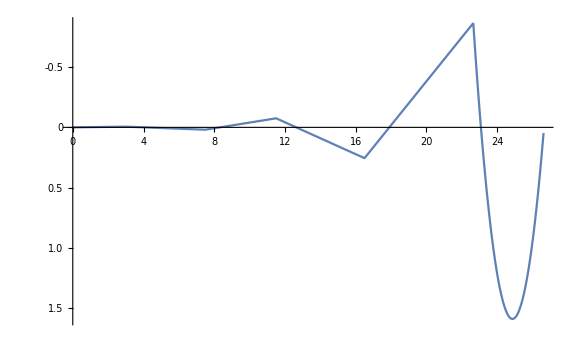

```mathematica
ListLinePlot[Table[{s[[i]], M[[6,i]]},{i,Length[s]}], ScalingFunctions->"Reverse",PlotRange->Full, ImageSize->Large]
```

```mathematica
1.3*(8+11.52+3.75)+1.5*(11.55+7.98+9.2)+1.5*(15.01)+1.5*.7*(7.5+14.40)+1.5*.6*.5
1*(8+11.52+3.75)+.8*(11.55+7.98+9.2)-1.5*.5

1.3*(8+6.72+3.75)+1.5*(11.55+4.65+9.2)+1.5*(10.30)+1.5*.7*(7.5+8.4)+1.5*.6*.3
1*(8+6.72+3.75)+.8*(11.55+4.65+9.2)-1.5*.3

1.3*(6+3.2+3.75)+1.5*(8.66+2.215+9.2)+1.5*(4.17)+1.5*.7*(5.63+4)+1.5*.6*.138
1*(6+3.2+3.75)+.8*(8.66+2.215+9.2)-1.5*.138
```

119.306

45.504

94.526

38.34

63.4382

28.803

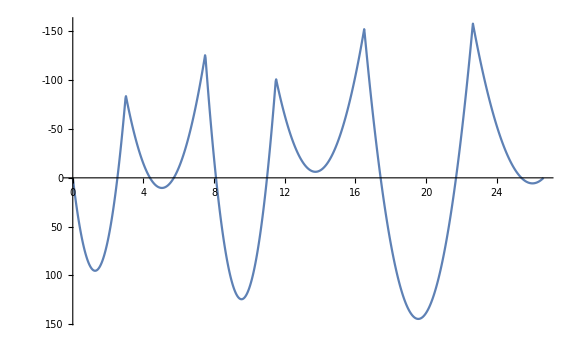

```mathematica
ClearAll[q1max,q1min,
q2max,q2min,
q3max,q3min,
q4max,q4min,
q5max,q5min,
q6max,q6min]
QEd ={
{119.306,45.504000000000005},
{119.306,45.504000000000005},
{119.306,45.504000000000005},
{94.52600000000001,38.34},
{63.438199999999995,28.802999999999997},
{63.438199999999995,28.802999999999997}
} ;
MatrixForm[%];
i=.;
j=.;

M1 = 0*Array[0, {Nc, Length[s]}];
For[i=1, i<=Nc, i++,
If[OddQ[i]==True,
{
k=1;
},
k=2;
];
M1[[i]] = QEd[[i, k]]*M[[i, All]]//Chop;
];
M1 = Sum[M1[[i, All]], {i, Length[M1]}];
ListLinePlot[Table[{s[[i]],M1[[i]]},{i,Length[s]}], ScalingFunctions->"Reverse",PlotRange->Full, ImageSize->Large]
```

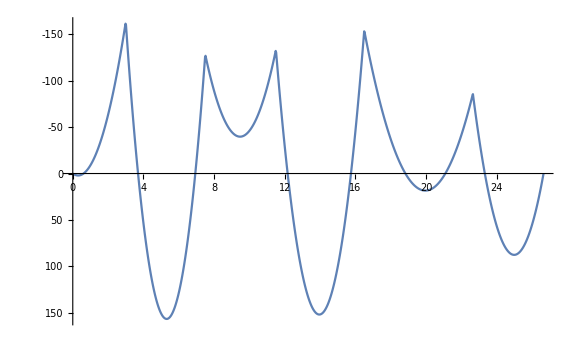

```mathematica
M2 = 0*Array[0, {Nc, Length[s]}];
For[i=1, i<=Nc, i++,
If[EvenQ[i]==True,
{
k=1;
},
k=2;
];
M2[[i]] = QEd[[i, k]]*M[[i, All]]//Chop;
];
M2 = Sum[M2[[i, All]], {i, Length[M2]}];
ListLinePlot[Table[{s[[i]],M2[[i]]},{i,Length[s]}], ScalingFunctions->"Reverse",PlotRange->Full, ImageSize->Large]
```

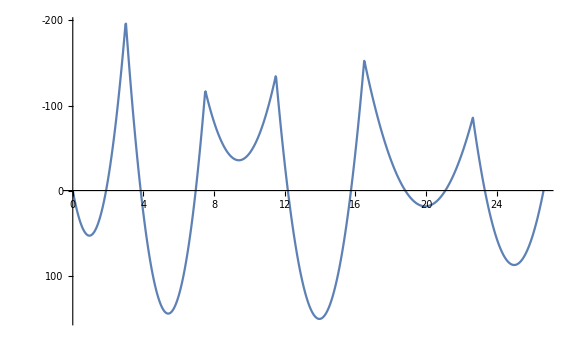

```mathematica
M3 = 0*Array[0, {Nc, Length[s]}];
For[i=1, i<=Nc, i++,
If[i==1,
k=1,
If[EvenQ[i]==True,
{
k=1;
},
k=2;
]
];
M3[[i]] = QEd[[i, k]]*M[[i, All]]//Chop;
];
M3 = Sum[M3[[i, All]], {i, Length[M3]}];
ListLinePlot[Table[{s[[i]],M3[[i]]},{i,Length[s]}], ScalingFunctions->"Reverse",PlotRange->Full, ImageSize->Large]
```

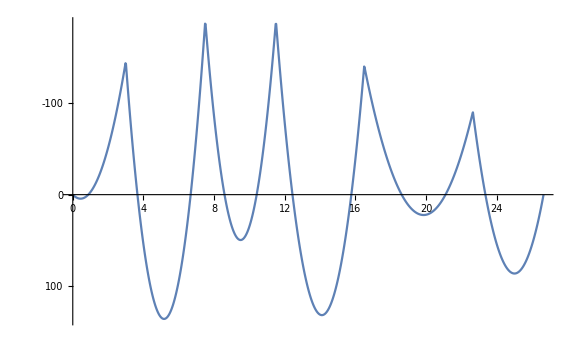

```mathematica
M4 = 0*Array[0, {Nc, Length[s]}];
For[i=1, i<=Nc, i++,
If[i==3,
k=1,
If[EvenQ[i]==True,
{
k=1;
},
k=2;
]
];
M4[[i]] = QEd[[i, k]]*M[[i, All]]//Chop;
];
M4 = Sum[M4[[i, All]], {i, Length[M4]}];
ListLinePlot[Table[{s[[i]],M4[[i]]},{i,Length[s]}], ScalingFunctions->"Reverse",PlotRange->Full, ImageSize->Large]
```

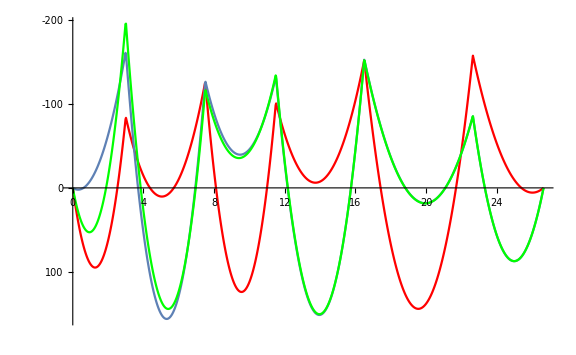

```mathematica
Show[
ListLinePlot[Table[{s[[i]],M1[[i]]},{i,Length[s]}], ScalingFunctions->"Reverse", PlotStyle->Red],
ListLinePlot[Table[{s[[i]],M2[[i]]},{i,Length[s]}], ScalingFunctions->"Reverse"],
ListLinePlot[Table[{s[[i]],M3[[i]]},{i,Length[s]}], ScalingFunctions->"Reverse", PlotStyle->Green],
PlotRange->Full, ImageSize->Large
]
```

```mathematica
combo=0*Array[0, {Nc+2}];
comboL=0*Array[0, {Nc}];
comboR=0*Array[0, {Nc}];
For[j=1, j<Nc, j++,
comboJ = {QEd[[j, 1]], QEd[[j+1, 1]]};
If[QuotientRemainder[j,2][[2]]==0,
{
For[i=j+2, i<=Nc, i++,
If[QuotientRemainder[i,2][[2]]!=0,
comboR[[i]] = QEd[[i,1]],
comboR[[i]] = QEd[[i, 2]]
];
];
For[i=1, i<=j+1, i++,
If[QuotientRemainder[i,2][[2]]==0,
comboL[[i]]= QEd[[i, 1]],
comboL[[i]] = QEd[[i,2]]
]
]
},
{
For[i=j+2, i<=Nc, i++,
If[QuotientRemainder[i,2][[2]]==0,
comboR[[i]] = QEd[[i,1]],
comboR[[i]] = QEd[[i, 2]]
];
];
For[i=1, i<j+1, i++,
If[QuotientRemainder[i,2][[2]]!=0,
comboL[[i]]= QEd[[i, 1]],
comboL[[i]] = QEd[[i,2]]
]
]
};
];
comboL = Join[comboL, comboJ];
comboL = Join[comboL, comboR];
combo = DeleteCases[comboL, 0, Infinity];

]
combo
QEd
```

{119.306,45.504,119.306,38.34,63.4382,119.306,119.306,45.504,94.526,28.803,63.4382,119.306,119.306,45.504,38.34,63.4382,28.803,119.306,94.526,45.504,38.34,28.803,63.4382,94.526,63.4382,45.504,38.34,28.803,28.803,63.4382,63.4382,45.504,38.34,28.803,28.803}

{{119.306,45.504},{119.306,45.504},{119.306,45.504},{94.526,38.34},{63.4382,28.803},{63.4382,28.803}}

```mathematica
comboR[[1;;2]]
```

{0,0}